```mathematica
H={{1,1},{1,-1}}/Sqrt[2];
X={{0,1},{1,0}};
Z={{1,0},{0,-1}};
Y={{0,-I},{I,0}};
CNOT={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}; 
NOTC={{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}; 
XNOTC={{0,0,1,0},{0,1,0,0},{1,0,0,0},{0,0,0,1}}; 
%//MatrixForm
Phase[phi_,pauli_]:=MatrixExp[I phi * pauli]
Phase[Pi/8,Z]//MatrixForm
KroneckerProduct[X,H];
%//MatrixForm
%[[{1,2},{2,3}]]//MatrixForm
NToffoli=IdentityMatrix[8];
NToffoli[[{1,2},{1,2}]]=X;
RevNToffoli=IdentityMatrix[8];
RevNToffoli[[{1,5},{1,5}]]=X;
```

(0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1)

(ⅇ^((ⅈ π)/8) | 0
0 | ⅇ^(-(ⅈ π)/8))

(0 | 0 | 1/(√2) | 1/(√2)
0 | 0 | 1/(√2) | -1/(√2)
1/(√2) | 1/(√2) | 0 | 0
1/(√2) | -1/(√2) | 0 | 0)

(0 | 1/(√2)
0 | 1/(√2))

(0.0322461064+0.4121121243 ⅈ | 0.0529849416-0.2854034061 ⅈ | 0.3723431723+0.229761637 ⅈ | 0.4369761703-0.0737237767 ⅈ
-0.4296936598-0.164528617 ⅈ | 0.4089548247+0.362044147 ⅈ | 0.2957024311-0.123791754 ⅈ | 0.139664571-0.2798296139 ⅈ
0.114276695+0.2703145555 ⅈ | -0.1875-0.178909693 ⅈ | -0.196491229+0.2465592057 ⅈ | -0.1740436753+0.0800815355 ⅈ
0.1684698831+0.0539096932 ⅈ | -0.2202465784+0.0417611649 ⅈ | -0.174043675-0.2758883476 ⅈ | 0.0051495125-0.4111873727 ⅈ)

{0.9950777362,0.9366083393,0.3503781081,0.09909742093}

0.+28.0314 x+0. x^2-266.764 x^3+0. x^4+477.465 x^5+0. x^6-238.732 x^7

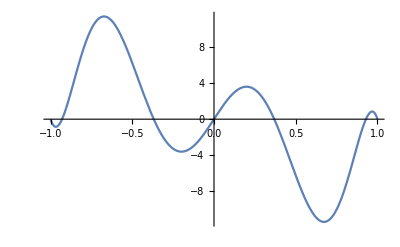

0.+8.1634 x-93.5352 x^3+301.218 x^5-363.174 x^7+147.483 x^9

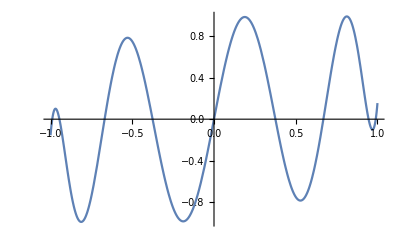

```mathematica
U=KroneckerProduct[NOTC,X].
KroneckerProduct[Phase[Pi/4,Y],Phase[Pi/8,Z],Phase[Pi/16,X]].
KroneckerProduct[Z,NOTC].
KroneckerProduct[Phase[Pi/16,Y],Phase[Pi/8,X],Phase[Pi/4,Y]].
KroneckerProduct[NOTC,Z].KroneckerProduct[Phase[Pi/4,X],Phase[Pi/8,Y],Phase[Pi/16,Z]].KroneckerProduct[X,NOTC].
KroneckerProduct[NOTC,Z].KroneckerProduct[Phase[Pi/16,Y],Phase[Pi/8,X],Phase[Pi/4,Z]];
A=U[[Range[1,4],Range[1,4]]]//N[#,10]&;
A//MatrixForm
SingularValueList[A]
(*Lowest degree problem specific polynomial*)
poly1=InterpolatingPolynomial[{#,1/(4#)}&/@Join[%,-%],x]//Simplify//Chop
Plot[poly1,{x,-1,1}]
(*Optimised problem specific polynomial*)
poly=InterpolatingPolynomial[Join[{#,1/(14#)}&/@Join[%%%,-%%%],{{-0.7,-0.3},{0.7,0.3}}],x];
poly=((poly- (poly/.x->-x))/2)//Simplify
Plot[poly,{x,-1,1}]
```

```mathematica
getPolyPairs[poly_,precision_]:=Module[{polyTry,K,roots,Qp,Zp,SRp,LRp,Ip,Wp,genRoots,zeroRoots,smallRealRoots,largeRealRoots,imgRoots,parityTrick,Bp,Cp},
polyTry=SetPrecision[poly,precision];
degree = (CoefficientList[polyTry,x]//Length)-1;
(K=Sqrt[-Coefficient[(1-polyTry^2//Expand),x^(2 degree)]])//Precision;
roots=x/.NSolve[(1-polyTry^2//Expand)==0,x,WorkingPrecision->precision];
(*p=ListPlot[{Re[#],Im[#]}&/@%,AxesOrigin->{0,0},PlotRange->{{-1.2,1.2},{-1.2,1.2}},ImagePadding->40,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]]];
Show[p,Graphics@Circle[{0,0},1]]*)
(genRoots=Select[roots,(Re[#]>0&& Im[#]>0)&]);
zeroRoots=(Select[roots,(#==0)&]);
smallRealRoots=(Select[roots,(#!=0&&Re[#]>-1&&Re[#]<1&& Im[#]==0)&]);
(smallRealRoots=Table[smallRealRoots[[4i-3]],{i,1,(smallRealRoots//Length)/4}]);
(largeRealRoots=Select[roots,(Re[#]≥1&& Im[#]==0)&]);
(imgRoots=Select[roots,(Re[#]==0&& Im[#]>0)&]);
Qp=(#[[2]]x^2-#[[1]]+I Sqrt[#[[2]]^2-1]x Sqrt[1-x^2])&/@({Abs[#]^2,Abs[#]^2+Sqrt[2(Re[#]^2+1)Im[#]^2+(Re[#]^2-1)^2+Im[#]^4]}&/@genRoots) ;
Zp=x^((zeroRoots//Length)/2);
SRp=(x^2-#^2)&/@smallRealRoots;
LRp=(Sqrt[#^2-1]x+I # Sqrt[1-x^2])&/@largeRealRoots;
Ip=(Sqrt[Abs[#]^2+1]x-I Abs[#]Sqrt[1-x^2])&/@imgRoots;
Wp=K*(Times@@Qp)*Zp*(Times@@SRp)*(Times@@LRp)*(Times@@Ip)//Expand//Simplify;
parityTrick=SetPrecision[Wp/.{Sqrt[1-x^2]->-I},precision];
Bp=SetPrecision[(parityTrick+(-1)^degree(parityTrick/.x->-x))/2//Simplify,parityTrick//Precision];
Cp=SetPrecision[(parityTrick-(-1)^degree(parityTrick/.x->-x))/2//Simplify,parityTrick//Precision];
{Bp,Cp}
]
{Bp,Cp}=getPolyPairs[ChebyshevT[5,x] ,110];
Bp^2+(1-x^2)Cp^2+ChebyshevT[5,x]^2//Expand//Chop;
(%//CoefficientList[#,x]&//Length)==1
{Bp,Cp}=getPolyPairs[poly,30];
poly=SetPrecision[poly,30];
Bp^2+(1-x^2)Cp^2+poly^2//Expand//Chop;
(%//CoefficientList[#,x]&//Length)==1
```

True

True

```mathematica
carveLastAngle[Mat_]:=Module[{angle,outMat},
angle=(Coefficient[Mat[[1,1]],x,Exponent[Mat[[1,1]],x]]/(Coefficient[Mat[[1,2]]/.{Sqrt[1-x^2]->-I},x,(Exponent[Mat[[1,1]],x]-1)]))//Sqrt;
outMat=Mat.{{Conjugate[angle],0},{0,angle}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand;
outMat=outMat/.x^b_/;b≥Exponent[Mat[[1,1]],x]+1->0;
outMat=outMat/.Sqrt[1-x^2]x^b_/;b≥Exponent[Mat[[1,1]],x]->0;
{outMat, angle}
];
getMatrix[phs_]:=Module[{phaseGates,W},
phaseGates=Table[{{phs[[i]],0},{0,Conjugate[phs[[i]]]}},{i,1,Length[phs]}];
(W={{x,I Sqrt[1-x^2]},{I Sqrt[1-x^2],x}})//MatrixForm;
(Dot@@((phaseGates//Most).W)).(phaseGates//Last)//Expand
];
getPhases[poly_,precision_]:=Module[{tmpPoly,agreement,tmpprecision,Bp,Cp,Mat,carved,phs,phaseGates,W,NewMat},
agreement=1;
tmpprecision=MachinePrecision;
phs={};
While[ ((agreement//Accuracy) <precision) ||(agreement>10^-precision),
tmpPoly=SetPrecision[poly,tmpprecision];
{Bp,Cp}=getPolyPairs[tmpPoly,tmpprecision];
(Mat={{tmpPoly+ I Bp,  Sqrt[1-x^2] Cp},{- Sqrt[1-x^2] Cp,tmpPoly-I Bp}})//MatrixForm;
carved=NestList[carveLastAngle[#[[1]]]&,{Mat,{}},(tmpPoly//CoefficientList[#,x]&//Length)-1];
phs=Join[{(carved//Last)[[1]][[1]][[1]]},(#[[2]]&/@ carved)//Reverse//Most];
NewMat=getMatrix[phs];
agreement=(NewMat[[1,1]]-tmpPoly-I Bp)//Expand//CoefficientList[#,x]&//Abs//Total;
Print[tmpprecision];
tmpprecision=2tmpprecision];
phs
];
phs=getPhases[ChebyshevT[10,x],20];
```

MachinePrecision

2 MachinePrecision

4 MachinePrecision

```mathematica
(Mat={{poly+ I Bp,  Sqrt[1-x^2] Cp},{- Sqrt[1-x^2] Cp,poly-I Bp}})
ph9=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop
ph8=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph7=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph6=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph5=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph4=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph3=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph2=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(Coefficient[%[[1,2]]/.{Sqrt[1-x^2]->-I},x^(Exponent[%[[1,1]],x]-1)])//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph1=Coefficient[%[[1,1]],x^Exponent[%[[1,1]],x]]/(%[[1,2]]/.{Sqrt[1-x^2]->-I})//Sqrt
%%.{{Conjugate[%],0},{0,%}}.{{x,-I Sqrt[1-x^2]},{-I Sqrt[1-x^2],x}}//Expand//Chop;
ph0=%[[1,1]]
(R={{x,Sqrt[1-x^2]},{Sqrt[1-x^2],-x}})//MatrixForm
phs={I*ph0*ph9,ph1,ph2,ph3,ph4,ph5,ph6,ph7,ph8}/I//Arg;
NewMat=Dot@@Table[Phase[phs[[i]],Z].R,{i,1,Length[phs]}]//Expand//Simplify;
NewMat[[1,1]]-poly-I Bp//Expand//CoefficientList[#,x]&//Norm[#,1]&
```

{{0.+8.1634 x-93.5352 x^3+301.218 x^5-363.174 x^7+147.483 x^9+ⅈ (2.653456008016759 x-53.93686761532925 x^3+223.9707737865158 x^5-326.2673768264304 x^7+154.5680162914525 x^9),√(1-x^2) (1.-36.34097647405764 x^2+210.0105110436473 x^4-379.9424126733127 x^6+213.6407384630828 x^8)},{-√(1-x^2) (1.-36.34097647405764 x^2+210.0105110436473 x^4-379.9424126733127 x^6+213.6407384630828 x^8),0.+8.1634 x-93.5352 x^3+301.218 x^5-363.174 x^7+147.483 x^9-ⅈ (2.653456008016759 x-53.93686761532925 x^3+223.9707737865158 x^5-326.2673768264304 x^7+154.5680162914525 x^9)}}

0.371823+0.928304 ⅈ

{{(0.928304-0.371823 ⅈ)-(29.1652-7.29274 ⅈ) x^2+(143.841-24.8251 ⅈ) x^4-(227.743-23.0139 ⅈ) x^6+(113.114-4.88576 ⅈ) x^8,(-6.21968-4.57025 ⅈ) x √(1-x^2)+(53.2617+51.1129 ⅈ) x^3 √(1-x^2)-(118.257+124.959 ⅈ) x^5 √(1-x^2)+(74.5508+85.2099 ⅈ) x^7 √(1-x^2)},{(6.21968-4.57025 ⅈ) x √(1-x^2)-(53.2617-51.1129 ⅈ) x^3 √(1-x^2)+(118.257-124.959 ⅈ) x^5 √(1-x^2)-(74.5508-85.2099 ⅈ) x^7 √(1-x^2),(0.928304+0.371823 ⅈ)-(29.1652+7.29274 ⅈ) x^2+(143.841+24.8251 ⅈ) x^4-(227.743+23.0139 ⅈ) x^6+(113.114+4.88576 ⅈ) x^8}}

0.943484+0.331418 ⅈ

0.993583+0.113104 ⅈ

0.997673+0.0681745 ⅈ

0.976776-0.214265 ⅈ

0.976776-0.214265 ⅈ

0.997673+0.0681745 ⅈ

0.993583+0.113104 ⅈ

0.943484+0.331418 ⅈ

0.928304-0.371823 ⅈ

(x | √(1-x^2)
√(1-x^2) | -x)

3.70222×10^-10

```mathematica
HHL=Dot@@Table[KroneckerProduct[XNOTC,IdentityMatrix[4]].KroneckerProduct[Phase[phs[[i]],Z],IdentityMatrix[8]].KroneckerProduct[XNOTC,IdentityMatrix[4]].KroneckerProduct[IdentityMatrix[2],MatrixPower[U//N,(-1)^i]],{i,1,Length[phs]}];
HHL=KroneckerProduct[H,IdentityMatrix[8]].HHL.KroneckerProduct[H,IdentityMatrix[8]];
HHL[[1;;4,1;;4]];
%//MatrixForm
(%%*14-AInv)//Norm
```

(0.123302+0.0612786 ⅈ | -0.152829-0.0961579 ⅈ | -0.285155-0.164685 ⅈ | 0.126288-0.179026 ⅈ
0.145875+0.0869695 ⅈ | -0.105248-0.107894 ⅈ | -0.321182-0.0670514 ⅈ | 0.0644302-0.211255 ⅈ
-0.0438065-0.122915 ⅈ | 0.101795+0.0066714 ⅈ | 0.141445-0.026424 ⅈ | -0.14997+0.0860774 ⅈ
0.092266+0.107257 ⅈ | -0.0831759+0.0223294 ⅈ | -0.18533-0.00368527 ⅈ | 0.126955-0.0112672 ⅈ)

Max[√Root[(954.93+2.72848×10^-12 ⅈ)-(615.69-92.3594 ⅈ) AInv-(8.12861×10^-12+2.72848×10^-12 ⅈ) AInv^2+(6.67299×10^-14+1.25527×10^-13 ⅈ) AInv^3-(615.69+92.3594 ⅈ) Conjugate[AInv]+(405.899+3.63798×10^-12 ⅈ) AInv Conjugate[AInv]-(1.81899×10^-12+3.86535×10^-12 ⅈ) AInv^2 Conjugate[AInv]-1.13687×10^-13 AInv^3 Conjugate[AInv]+(2.84217×10^-13+3.35376×10^-12 ⅈ) Conjugate[AInv]^2+(6.36646×10^-12-9.89075×10^-12 ⅈ) AInv Conjugate[AInv]^2-(2.27374×10^-13+4.54747×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2+(0.+1.00974×10^-28 ⅈ) AInv^3 Conjugate[AInv]^2-(1.63413×10^-13+3.6539×10^-13 ⅈ) Conjugate[AInv]^3+(8.55151×10^-14-7.47751×10^-14 ⅈ) AInv Conjugate[AInv]^3-(1.17771×10^-13-9.6199×10^-13 ⅈ) AInv^2 Conjugate[AInv]^3+((-1909.86+1.13687×10^-12 ⅈ)+(466.665+243.704 ⅈ) AInv+(2.27374×10^-13+2.27374×10^-13 ⅈ) AInv^2+(466.665-243.704 ⅈ) Conjugate[AInv]-(1659.03+6.82121×10^-13 ⅈ) AInv Conjugate[AInv]-(9.09495×10^-13+4.54747×10^-13 ⅈ) AInv^2 Conjugate[AInv]+(5.68434×10^-13+3.12639×10^-13 ⅈ) Conjugate[AInv]^2-(2.27374×10^-13+4.54747×10^-13 ⅈ) AInv Conjugate[AInv]^2+(2.27374×10^-13-2.27374×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2-(2.97061×10^-14-6.37224×10^-14 ⅈ) Conjugate[AInv]^3+(7.08942×10^-15+2.61783×10^-14 ⅈ) AInv Conjugate[AInv]^3-2.84217×10^-14 AInv^2 Conjugate[AInv]^3) #1+((1067.05+7.10543×10^-15 ⅈ)+(116.609-308.161 ⅈ) AInv-(1.42109×10^-14+5.32907×10^-15 ⅈ) AInv^2+(116.609+308.161 ⅈ) Conjugate[AInv]+(990.532-7.10543×10^-15 ⅈ) AInv Conjugate[AInv]+(7.10543×10^-15-7.10543×10^-15 ⅈ) AInv^2 Conjugate[AInv]-(1.42109×10^-14-1.42109×10^-14 ⅈ) Conjugate[AInv]^2+1.77636×10^-14 AInv Conjugate[AInv]^2) #1^2+(-112.125-(5.66075-8.67688 ⅈ) AInv-(5.66075+8.67688 ⅈ) Conjugate[AInv]-16. AInv Conjugate[AInv]) #1^3+1. #1^4&,1],√Root[(954.93+2.72848×10^-12 ⅈ)-(615.69-92.3594 ⅈ) AInv-(8.12861×10^-12+2.72848×10^-12 ⅈ) AInv^2+(6.67299×10^-14+1.25527×10^-13 ⅈ) AInv^3-(615.69+92.3594 ⅈ) Conjugate[AInv]+(405.899+3.63798×10^-12 ⅈ) AInv Conjugate[AInv]-(1.81899×10^-12+3.86535×10^-12 ⅈ) AInv^2 Conjugate[AInv]-1.13687×10^-13 AInv^3 Conjugate[AInv]+(2.84217×10^-13+3.35376×10^-12 ⅈ) Conjugate[AInv]^2+(6.36646×10^-12-9.89075×10^-12 ⅈ) AInv Conjugate[AInv]^2-(2.27374×10^-13+4.54747×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2+(0.+1.00974×10^-28 ⅈ) AInv^3 Conjugate[AInv]^2-(1.63413×10^-13+3.6539×10^-13 ⅈ) Conjugate[AInv]^3+(8.55151×10^-14-7.47751×10^-14 ⅈ) AInv Conjugate[AInv]^3-(1.17771×10^-13-9.6199×10^-13 ⅈ) AInv^2 Conjugate[AInv]^3+((-1909.86+1.13687×10^-12 ⅈ)+(466.665+243.704 ⅈ) AInv+(2.27374×10^-13+2.27374×10^-13 ⅈ) AInv^2+(466.665-243.704 ⅈ) Conjugate[AInv]-(1659.03+6.82121×10^-13 ⅈ) AInv Conjugate[AInv]-(9.09495×10^-13+4.54747×10^-13 ⅈ) AInv^2 Conjugate[AInv]+(5.68434×10^-13+3.12639×10^-13 ⅈ) Conjugate[AInv]^2-(2.27374×10^-13+4.54747×10^-13 ⅈ) AInv Conjugate[AInv]^2+(2.27374×10^-13-2.27374×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2-(2.97061×10^-14-6.37224×10^-14 ⅈ) Conjugate[AInv]^3+(7.08942×10^-15+2.61783×10^-14 ⅈ) AInv Conjugate[AInv]^3-2.84217×10^-14 AInv^2 Conjugate[AInv]^3) #1+((1067.05+7.10543×10^-15 ⅈ)+(116.609-308.161 ⅈ) AInv-(1.42109×10^-14+5.32907×10^-15 ⅈ) AInv^2+(116.609+308.161 ⅈ) Conjugate[AInv]+(990.532-7.10543×10^-15 ⅈ) AInv Conjugate[AInv]+(7.10543×10^-15-7.10543×10^-15 ⅈ) AInv^2 Conjugate[AInv]-(1.42109×10^-14-1.42109×10^-14 ⅈ) Conjugate[AInv]^2+1.77636×10^-14 AInv Conjugate[AInv]^2) #1^2+(-112.125-(5.66075-8.67688 ⅈ) AInv-(5.66075+8.67688 ⅈ) Conjugate[AInv]-16. AInv Conjugate[AInv]) #1^3+1. #1^4&,2],√Root[(954.93+2.72848×10^-12 ⅈ)-(615.69-92.3594 ⅈ) AInv-(8.12861×10^-12+2.72848×10^-12 ⅈ) AInv^2+(6.67299×10^-14+1.25527×10^-13 ⅈ) AInv^3-(615.69+92.3594 ⅈ) Conjugate[AInv]+(405.899+3.63798×10^-12 ⅈ) AInv Conjugate[AInv]-(1.81899×10^-12+3.86535×10^-12 ⅈ) AInv^2 Conjugate[AInv]-1.13687×10^-13 AInv^3 Conjugate[AInv]+(2.84217×10^-13+3.35376×10^-12 ⅈ) Conjugate[AInv]^2+(6.36646×10^-12-9.89075×10^-12 ⅈ) AInv Conjugate[AInv]^2-(2.27374×10^-13+4.54747×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2+(0.+1.00974×10^-28 ⅈ) AInv^3 Conjugate[AInv]^2-(1.63413×10^-13+3.6539×10^-13 ⅈ) Conjugate[AInv]^3+(8.55151×10^-14-7.47751×10^-14 ⅈ) AInv Conjugate[AInv]^3-(1.17771×10^-13-9.6199×10^-13 ⅈ) AInv^2 Conjugate[AInv]^3+((-1909.86+1.13687×10^-12 ⅈ)+(466.665+243.704 ⅈ) AInv+(2.27374×10^-13+2.27374×10^-13 ⅈ) AInv^2+(466.665-243.704 ⅈ) Conjugate[AInv]-(1659.03+6.82121×10^-13 ⅈ) AInv Conjugate[AInv]-(9.09495×10^-13+4.54747×10^-13 ⅈ) AInv^2 Conjugate[AInv]+(5.68434×10^-13+3.12639×10^-13 ⅈ) Conjugate[AInv]^2-(2.27374×10^-13+4.54747×10^-13 ⅈ) AInv Conjugate[AInv]^2+(2.27374×10^-13-2.27374×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2-(2.97061×10^-14-6.37224×10^-14 ⅈ) Conjugate[AInv]^3+(7.08942×10^-15+2.61783×10^-14 ⅈ) AInv Conjugate[AInv]^3-2.84217×10^-14 AInv^2 Conjugate[AInv]^3) #1+((1067.05+7.10543×10^-15 ⅈ)+(116.609-308.161 ⅈ) AInv-(1.42109×10^-14+5.32907×10^-15 ⅈ) AInv^2+(116.609+308.161 ⅈ) Conjugate[AInv]+(990.532-7.10543×10^-15 ⅈ) AInv Conjugate[AInv]+(7.10543×10^-15-7.10543×10^-15 ⅈ) AInv^2 Conjugate[AInv]-(1.42109×10^-14-1.42109×10^-14 ⅈ) Conjugate[AInv]^2+1.77636×10^-14 AInv Conjugate[AInv]^2) #1^2+(-112.125-(5.66075-8.67688 ⅈ) AInv-(5.66075+8.67688 ⅈ) Conjugate[AInv]-16. AInv Conjugate[AInv]) #1^3+1. #1^4&,3],√Root[(954.93+2.72848×10^-12 ⅈ)-(615.69-92.3594 ⅈ) AInv-(8.12861×10^-12+2.72848×10^-12 ⅈ) AInv^2+(6.67299×10^-14+1.25527×10^-13 ⅈ) AInv^3-(615.69+92.3594 ⅈ) Conjugate[AInv]+(405.899+3.63798×10^-12 ⅈ) AInv Conjugate[AInv]-(1.81899×10^-12+3.86535×10^-12 ⅈ) AInv^2 Conjugate[AInv]-1.13687×10^-13 AInv^3 Conjugate[AInv]+(2.84217×10^-13+3.35376×10^-12 ⅈ) Conjugate[AInv]^2+(6.36646×10^-12-9.89075×10^-12 ⅈ) AInv Conjugate[AInv]^2-(2.27374×10^-13+4.54747×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2+(0.+1.00974×10^-28 ⅈ) AInv^3 Conjugate[AInv]^2-(1.63413×10^-13+3.6539×10^-13 ⅈ) Conjugate[AInv]^3+(8.55151×10^-14-7.47751×10^-14 ⅈ) AInv Conjugate[AInv]^3-(1.17771×10^-13-9.6199×10^-13 ⅈ) AInv^2 Conjugate[AInv]^3+((-1909.86+1.13687×10^-12 ⅈ)+(466.665+243.704 ⅈ) AInv+(2.27374×10^-13+2.27374×10^-13 ⅈ) AInv^2+(466.665-243.704 ⅈ) Conjugate[AInv]-(1659.03+6.82121×10^-13 ⅈ) AInv Conjugate[AInv]-(9.09495×10^-13+4.54747×10^-13 ⅈ) AInv^2 Conjugate[AInv]+(5.68434×10^-13+3.12639×10^-13 ⅈ) Conjugate[AInv]^2-(2.27374×10^-13+4.54747×10^-13 ⅈ) AInv Conjugate[AInv]^2+(2.27374×10^-13-2.27374×10^-13 ⅈ) AInv^2 Conjugate[AInv]^2-(2.97061×10^-14-6.37224×10^-14 ⅈ) Conjugate[AInv]^3+(7.08942×10^-15+2.61783×10^-14 ⅈ) AInv Conjugate[AInv]^3-2.84217×10^-14 AInv^2 Conjugate[AInv]^3) #1+((1067.05+7.10543×10^-15 ⅈ)+(116.609-308.161 ⅈ) AInv-(1.42109×10^-14+5.32907×10^-15 ⅈ) AInv^2+(116.609+308.161 ⅈ) Conjugate[AInv]+(990.532-7.10543×10^-15 ⅈ) AInv Conjugate[AInv]+(7.10543×10^-15-7.10543×10^-15 ⅈ) AInv^2 Conjugate[AInv]-(1.42109×10^-14-1.42109×10^-14 ⅈ) Conjugate[AInv]^2+1.77636×10^-14 AInv Conjugate[AInv]^2) #1^2+(-112.125-(5.66075-8.67688 ⅈ) AInv-(5.66075+8.67688 ⅈ) Conjugate[AInv]-16. AInv Conjugate[AInv]) #1^3+1. #1^4&,4]]

```mathematica
AInv=Inverse[A]
NA=Table[(Abs[#^2]&)/@(AInv.IdentityMatrix[4][[k]]//Normalize),{k,1,4}]//Transpose;
NA//MatrixForm
BarChart3D[(*Reverse/@*)NA//Transpose,ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"Canvas"->False,"FaceGrids"->None][[1]]//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&
```

{{1.72623+0.8579 ⅈ,-2.13961-1.34621 ⅈ,-3.99217-2.30559 ⅈ,1.76803-2.50636 ⅈ},{2.04225+1.21757 ⅈ,-1.47347-1.51052 ⅈ,-4.49654-0.938719 ⅈ,0.902023-2.95757 ⅈ},{-0.613291-1.72081 ⅈ,1.42513+0.0933997 ⅈ,1.98023-0.369936 ⅈ,-2.09958+1.20508 ⅈ},{1.29172+1.5016 ⅈ,-1.16446+0.312612 ⅈ,-2.59462-0.0515938 ⅈ,1.77737-0.157741 ⅈ}}

(0.223445 | 0.445733 | 0.399901 | 0.335836
0.339949 | 0.310592 | 0.39702 | 0.3413
0.200683 | 0.142276 | 0.0763586 | 0.209205
0.235923 | 0.101399 | 0.12672 | 0.113659)

-Graphics3D-

```mathematica
AInv//Round[#,0.1]&//MatrixForm
BarChart3D[(*Reverse/@*)AInv//Transpose//Abs//#^1&,ChartLayout->"Grid",BarSpacing->{0,0},ChartElementFunction->ChartElementDataFunction["GradientScaleCube","ColorScheme"->"Rainbow"],"Canvas"->False,"FaceGrids"->None][[1]]//Graphics3D[#,Axes->True,BoxRatios->{1,1,1/GoldenRatio}]&
```

(1.7+0.9 ⅈ | -2.1-1.3 ⅈ | -4.-2.3 ⅈ | 1.8-2.5 ⅈ
2.+1.2 ⅈ | -1.5-1.5 ⅈ | -4.5-0.9 ⅈ | 0.9-3. ⅈ
-0.6-1.7 ⅈ | 1.4+0.1 ⅈ | 2.-0.4 ⅈ | -2.1+1.2 ⅈ
1.3+1.5 ⅈ | -1.2+0.3 ⅈ | -2.6-0.1 ⅈ | 1.8-0.2 ⅈ)

-Graphics3D-